S. Patomäki 2016, 2017
sofia.patomaki@helsinki.fi

```mathematica
If[FreeQ[$Path,"/pathToQuantumMechanics.m/"],
AppendTo[$Path,"/pathToQuantumMechanics.m/"];
];
Needs["QuantumMechanics`"];
```

Import the Cooper Pair Box (CPB) transition energies (as a function of the phase) computed in CPBNumericalDiagonalization.nb

```mathematica
NotebookDirectory[]
```

/Users/ffia/Documents/Aalto_Quantum_driving/Pro_Gradu_VX/numerical/

```mathematica
SetDirectory[NotebookDirectory[]];
Energyeg=Flatten[Import["CPBEnergyeg.dat","Table"]];
phiList=Flatten[Import["CPBphiList.dat","Table"]];
```

Parameters:

```mathematica
Clear[vr1,vr2,vr,gqr1,gqr2,gqr];
vr1=4.79;
vr2=8.05;
vr={vr1,vr2}; (*Resonator resonance frequencies*)

gqr1=0.212;
gqr2=0.491;
gqr={{gqr1},{gqr2}}; (*Qubit-resonator coupling constants*)
```

Numerically diagonalize the Jaynes-Cummings-like Hamiltonian with a CPB and two LC-oscillator-resonators.
We use the rotating wave approximation, and take h = hbar = 1.
The Hamiltonian definitions are perhaps needlessly general (allowing for several qubits and resonators, with a wanted number of quanta in each). We first write down the subsystem Hamiltonian, and then form the appropriate tensor products. We sum the free qubit and resonator Hamiltonians with the interaction Hamiltonian.

```mathematica
Clear[NQubits,NResonators,NQuantaQubit,NQuantaResonator,NQuanta,eQubit,eResonator,
       HQubitSubsystem,HQubit,H1,HResonatorSubsystem,HResonator,H2,Hint,Hint1,Hint2,Hamiltonian];
NQubits=1; (*Number of qubits*)
NResonators=2; (*Number of resonators*)
NQuantaQubit=2; (*Ground and excited states*)
NQuantaResonator=3; (*Formally; should be infinite*)
NQuanta={NQuantaQubit,NQuantaResonator,NQuantaResonator};
eQubit=eList[NQuantaQubit];
eResonator=eList[NQuantaResonator];

(*Loop over phase*)
EigVals=Table[0,{i,1,Length[phiList]}];
EigVecs=Table[0,{i,1,Length[phiList]}];
Do[
  (*Free qubit Hamiltonian, with the ground state energy taken to be zero*)
  HQubit=Table[0,{i,1,NQubits}];
  HQubitSubsystem=Table[0,{i,1,NQubits}];
  Do[
    HQubitSubsystem[[q]]=Energyeg[[i]]×KetBraM[NQuantaQubit,2,2];
  ,{q,1,NQubits}];
  Do[
    HQubit[[q]]=1;
    Do[
    If[q==s,
    HQubit[[q]]=ArrayFlatten[TensorProduct[HQubit[[q]],HQubitSubsystem[[s]]]],
    HQubit[[q]]=ArrayFlatten[TensorProduct[HQubit[[q]],IdM[NQuantaResonator]]]
    ];
    ,{s,1,NResonators+NQubits}];
  ,{q,1,NQubits}];
  H1=Sum[HQubit[[q]],{q,1,NQubits}];
  (*A simpler definition:*)
  (*HQubit=Energyeg[[i]]×ArrayFlatten[TensorProduct[ArrayFlatten[TensorProduct[KetBraM[NQuantaQubit,2,2],IdM[NQuantaResonator]]],IdM[NQuantaResonator]]];*)

  (*Free resonator Hamiltonians*)
  HResonatorSubsystem=Table[0,{r,1,NResonators}];
  HResonator=Table[0,{r,1,NResonators}];
  Do[
    HResonatorSubsystem[[r]]=vr[[r]]×RaiseM[NQuantaResonator].LowerM[NQuantaResonator]
  ,{r,1,NResonators}];
  Do[
    HResonator[[r]]=1;
    Do[
      If[r+NQubits==s,
        HResonator[[r]]=ArrayFlatten[TensorProduct[HResonator[[r]],HResonatorSubsystem[[r]]]], 
        HResonator[[r]]=ArrayFlatten[TensorProduct[HResonator[[r]],IdM[NQuanta[[s]]]]]
      ];
    ,{s,1,NResonators+NQubits}]
  ,{r,1,NResonators}];
  H2=Sum[HResonator[[r]],{r,1,NResonators}];

  (*Interaction term*)
  Clear[Hint1,Hint2,Hint];
  Hint=Table[0,{q,1,NQubits},{r,1,NResonators}];
  Hint1=Table[0,{q,1,NQubits},{r,1,NResonators}];
  Hint2=Table[0,{q,1,NQubits},{r,1,NResonators}];
  Do[
    Do[
      Hint1[[q,r]]=1;
      Hint2[[q,r]]=1;
      Do[
        If[s==q,
        Hint1[[q,r]]=ArrayFlatten[TensorProduct[Hint1[[q,r]],KetBraM[NQuantaQubit,2,1]]];
        Hint2[[q,r]]=ArrayFlatten[TensorProduct[Hint2[[q,r]],KetBraM[NQuantaQubit,1,2]]],
        If[s==r+NQubits,
          Hint1[[q,r]]=ArrayFlatten[TensorProduct[Hint1[[q,r]],LowerM[NQuanta[[s]]]]];
          Hint2[[q,r]]=ArrayFlatten[TensorProduct[Hint2[[q,r]],RaiseM[NQuanta[[s]]]]],
          Hint1[[q,r]]=ArrayFlatten[TensorProduct[Hint1[[q,r]],IdM[NQuanta[[s]]]]];
          Hint2[[q,r]]=ArrayFlatten[TensorProduct[Hint2[[q,r]],IdM[NQuanta[[s]]]]] 
          ]
        ]
      ,{s,1,NQubits+NResonators}];
      Hint1[[q,r]]=Hint1[[q,r]]×gqr[[r,q]];
      Hint2[[q,r]]=Hint2[[q,r]]×gqr[[r,q]];
      Hint[[q,r]]=Hint1[[q,r]]+Hint2[[q,r]]
    ,{q,1,NQubits}]
  ,{r,1,NResonators}];
  H12=Sum[Sum[Hint[[q,r]],{q,1,NQubits}],{r,1,NResonators}];
  
  Hamiltonian=H1+H2+H12;
  {EigVals[[i]],EigVecs[[i]]}=Eigensystem[Hamiltonian,Cubics->True];
  
,{i,1,Length[phiList]}]
```

The eigenvalues are listed from largest to smallest y default.

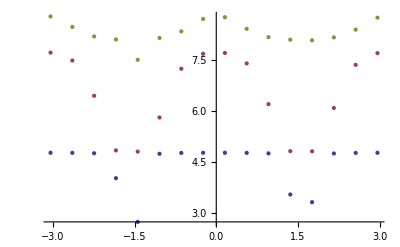

```mathematica
ListPlot[
{
Table[{phiList[[j]],EigVals[[j]][[-2]]},{j,1,Length[phiList]}][[2;;-1;;4]],
Table[{phiList[[j]],EigVals[[j]][[-3]]},{j,1,Length[phiList]}][[2;;-1;;4]],
Table[{phiList[[j]],EigVals[[j]][[-4]]},{j,1,Length[phiList]}][[2;;-1;;4]]
}
]
```